```mathematica
Integrate[ρ^(-1/2)Exp[ⅈ A ρ],{ρ,0,∞},Assumptions->{Im[A]>0}]
```

(√π)/(√(-ⅈ A))

```mathematica
Solve[{x t == Subscript[s, 1], t(1-x )== ⅈ Subscript[s, 2]},{x,t}]
```

{{x→s_1/(s_1+ⅈ s_2),t→s_1+ⅈ s_2}}

```mathematica
ComplexExpand[Subscript[s, 1]/(Subscript[s, 1]+ⅈ Subscript[s, 2])]
```

s_1^2/(s_1^2+s_2^2)-(ⅈ s_1 s_2)/(s_1^2+s_2^2)

```mathematica
Solve[{Subscript[x, 1]==x,Subscript[x, 2]==(1-x),y},{x,y}]
```

Solve[{x_1==x,x_2==1-x,y},{x,y}]

```mathematica
Solve[x(1-x)k^2+x M1 + (1-x)M2==0,x]
Solve[x(1-x)k^2+(1-x) M1 + x M2==0,x]
```

{{x→(k^2+M1-M2+√((k^2+M1-M2)^2+4 k^2 M2))/(2 k^2)},{x→-(-k^2-M1+M2+√((k^2+M1-M2)^2+4 k^2 M2))/(2 k^2)}}

{{x→-(-k^2+M1-M2+√(4 k^2 M1+(k^2-M1+M2)^2))/(2 k^2)},{x→(k^2-M1+M2+√(4 k^2 M1+(k^2-M1+M2)^2))/(2 k^2)}}

```mathematica
-k^2(x-x1)(x-x2)/.{x1-> (k^2+M1-M2+√((k^2+M1-M2)^2+4 k^2 M2))/(2 k^2),x2->(k^2+M1-M2-√((k^2+M1-M2)^2+4 k^2 M2))/(2 k^2)}//FullSimplify
```

M2-M2 x+(M1-k^2 (-1+x)) x

```mathematica
ComplexExpand[4 k^2 M1+(k^2-M1+M2)^2,{M1,M2}]
```

k^4-Im[M1]^2+2 Im[M1] Im[M2]-Im[M2]^2+2 k^2 Re[M1]+Re[M1]^2+2 k^2 Re[M2]-2 Re[M1] Re[M2]+Re[M2]^2+ⅈ (2 k^2 Im[M1]+2 k^2 Im[M2]+2 Im[M1] Re[M1]-2 Im[M2] Re[M1]-2 Im[M1] Re[M2]+2 Im[M2] Re[M2])

```mathematica
D[(2 k^2 Im[M1]+2 k^2 Im[M2]+2 Im[M1] Re[M1]-2 Im[M2] Re[M1]-2 Im[M1] Re[M2]+2 Im[M2] Re[M2])]
```

```mathematica
res1=Integrate[1/(√(x(1-x)k^2+m1 x + m2 (1-x))),x]
```

(ⅈ Log[-(ⅈ (-k^2-m1+m2+2 k^2 x))/k+2 √(m2+k^2 x+m1 x-m2 x-k^2 x^2)])/k

```mathematica
ComplexPlot[]
```

```mathematica
Series[res1,{x, ∞,0}]
Series[res1,{x, -∞,0}]
```

(ⅈ Log[2 (-ⅈ k x+√(-k^2 x^2))])/k+O[1/x]^1

(ⅈ Log[2 (-ⅈ k x+√(-k^2 x^2))])/k+O[1/x]^1

```mathematica
res=Integrate[1/(√(x(1-x)k^2+m1 x + m2 (1-x)))/.x-> ⅈ y,y]
```

Log[(ⅈ k^2+ⅈ m1-ⅈ m2+2 k^2 y)/k+2 √(m2+ⅈ k^2 y+ⅈ m1 y-ⅈ m2 y+k^2 y^2)]/k

```mathematica
Series[res,{y, ∞,0}]
Series[res,{y, -∞,0}]
```

Log[2 (k y+√(k^2 y^2))]/k+O[1/y]^1

Log[2 (k y+√(k^2 y^2))]/k+O[1/y]^1

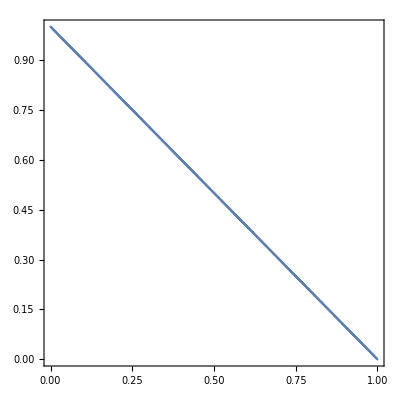

```mathematica
RegionPlot[x+y==1,{x,0,1},{y,0,1}]
```

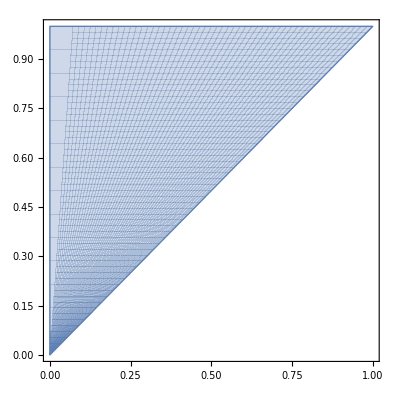

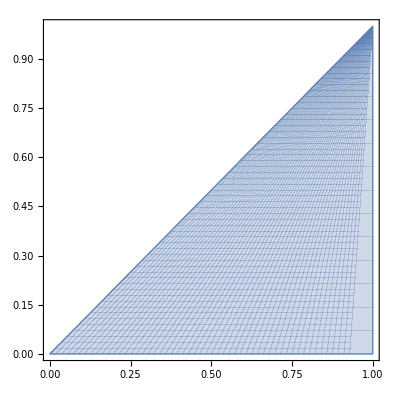

```mathematica
ParametricPlot[{y,x},{x,0,1},{y,0,x}]
ParametricPlot[{y,x},{x,0,1},{y,x,1}]
```

```mathematica
res =  -Integrate[(x(A+M1)(1+ⅈ Subscript[ϵ, 1])-(1-x)(B+M2)(1-ⅈ Subscript[ϵ, 2]))^-2,x]
```

-1/(((A+M1) ϵ_1-ⅈ (A+B+M1+M2-ⅈ (B+M2) ϵ_2)) ((A+M1) x ϵ_1-ⅈ (-M2+B (-1+x)+A x+M1 x+M2 x-ⅈ (B+M2) (-1+x) ϵ_2)))

```mathematica
(res/.x-> 1/.{Subscript[ϵ, 1]-> 0,Subscript[ϵ, 2]-> 0})-(res/.x-> 0/.{Subscript[ϵ, 1]-> 0,Subscript[ϵ, 2]-> 0})//FullSimplify
```

1/((A+M1) (B+M2))

```mathematica
Subscript[x, 3]=1-Subscript[x, 1]-Subscript[x, 2];
II =Subscript[x, 1] Subscript[x, 2] k1^2 - Subscript[x, 2] Subscript[x, 3] k2^2-Subscript[x, 1] Subscript[x, 3] k3^2+(2(Subscript[x, 1]+Subscript[x, 2])-1)(Subscript[x, 1] m1 + Subscript[x, 2] m2 - Subscript[x, 3] m3);
F = 2(Subscript[x, 1]+Subscript[x, 2])-1+ⅈ ϵ;
```

```mathematica
Series[F/( II)^(3/2)/.{Subscript[x, 2]-> 1/2-Subscript[x, 1]}//Simplify,{ϵ,0,1}]
```

(8 ⅈ ϵ)/((-k2^2+2 (k1^2+k2^2-k3^2) x_1-4 k1^2 x_1^2)^(3/2))+O[ϵ]^2

```mathematica
F/( II)^(3/2)/.{Subscript[x, 2]-> 1/2-Subscript[x, 1]}//Simplify
```

(8 ⅈ ϵ)/((-k2^2+2 (k1^2+k2^2-k3^2) x_1-4 k1^2 x_1^2)^(3/2))

```mathematica
Solve[{Subscript[x, 1]==(1-x)/(1-y)},{y}]
```

{{y→(-1+x+x_1)/x_1}}

```mathematica
D[x/(1-y),x]
D[x/(1-y),y]
D[1-x+y,x]
D[1-x+y,y]
```

1/(1-y)

x/(1-y)^2

-1

1

```mathematica
Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3])(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3)/.{Subscript[x, 3]->1-Subscript[x, 1]-Subscript[x, 2]}
```

m1 x_1+m3 (1-x_1-x_2)+k3^2 x_1 (1-x_1-x_2)+m2 x_2+k1^2 x_1 x_2+k2^2 (1-x_1-x_2) x_2

```mathematica
Subscript[x, 1] Subscript[x, 2] k1^2 - Subscript[x, 2] Subscript[x, 3] k2^2-Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3])(Subscript[x, 1] m1 + Subscript[x, 2] m2 - Subscript[x, 3] m3)/.{Subscript[x, 3]->Subscript[x, 1]+Subscript[x, 2]-1}
```

-m3+k3^2 x_1-m1 x_1+3 m3 x_1-k3^2 x_1^2+2 m1 x_1^2-2 m3 x_1^2+k2^2 x_2-m2 x_2+3 m3 x_2+k1^2 x_1 x_2-k2^2 x_1 x_2-k3^2 x_1 x_2+2 m1 x_1 x_2+2 m2 x_1 x_2-4 m3 x_1 x_2-k2^2 x_2^2+2 m2 x_2^2-2 m3 x_2^2

```mathematica
Subscript[x, 1] Subscript[x, 2] k1^2 - Subscript[x, 2] Subscript[x, 3] k2^2-Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3])(Subscript[x, 1] m1 + Subscript[x, 2] m2 - Subscript[x, 3] m3)/.{Subscript[x, 3]->Subscript[x, 1]+Subscript[x, 2]+1}//FullSimplify
```

k1^2 x_1 x_2-k3^2 x_1 (1+x_1+x_2)-k2^2 x_2 (1+x_1+x_2)+(-1+2 x_1+2 x_2) (m1 x_1+m2 x_2-m3 (1+x_1+x_2))

```mathematica
(Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3))/.{Subscript[x, 3]-> 1-Subscript[x, 2]-Subscript[x, 1]}/.{Subscript[x, 1]-> x/(1-y),Subscript[x, 2]->1- x+y}//Simplify
```

(m1 x)/(1-y)+(k1^2 x (-1+x-y))/(-1+y)-(k3^2 x (1+x-y) y)/(-1+y)^2+(m3 (1+x-y) y)/(-1+y)-(k2^2 (-1+x-y) (1+x-y) y)/(-1+y)+m2 (1-x+y)

```mathematica
(m2 x+m1 (-1+x) (-1+y)+k1^2 (-1+x) x (-1+y)-(k3^2+m3) y+(-2 m2+m3-k3^2 (-2+x)+k2^2 (-1+x)) x y+(m3-m3 x+x (k2^2+m2-k2^2 x)) y^2)//Expand
```

m1+k1^2 x-m1 x+m2 x-k1^2 x^2-k3^2 y-m1 y-m3 y-k1^2 x y-k2^2 x y+2 k3^2 x y+m1 x y-2 m2 x y+m3 x y+k1^2 x^2 y+k2^2 x^2 y-k3^2 x^2 y+m3 y^2+k2^2 x y^2+m2 x y^2-m3 x y^2-k2^2 x^2 y^2

```mathematica
(Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3))/.{Subscript[x, 3]-> 1-Subscript[x, 2]-Subscript[x, 1]}/.{Subscript[x, 1]-> x,Subscript[x, 2]-> (1-x)y}//Expand
```

m3+k3^2 x+m1 x-m3 x-k3^2 x^2+k2^2 y+m2 y-m3 y+k1^2 x y-2 k2^2 x y-k3^2 x y-m2 x y+m3 x y-k1^2 x^2 y+k2^2 x^2 y+k3^2 x^2 y-k2^2 y^2+2 k2^2 x y^2-k2^2 x^2 y^2

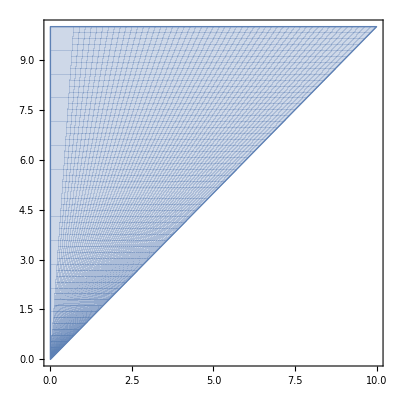

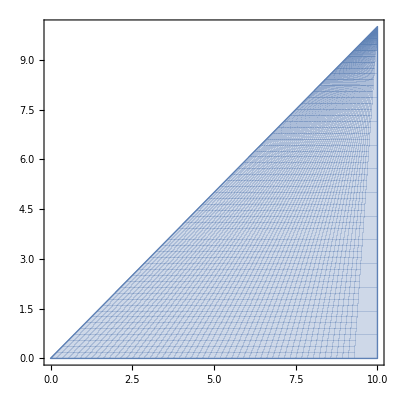

```mathematica
ParametricPlot[{x,y},{y,0,10},{x,0,y}]
ParametricPlot[{x,y},{y,0,10},{x,y,10}]
```

```mathematica
Solve[{x1==x,x2==-(1-x)y},{x,y}]
```

{{x→x1,y→x2/(-1+x1)}}

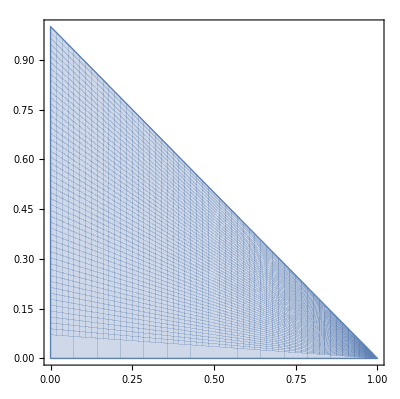

```mathematica
ParametricPlot[{x1,x2},{x1,0,1},{x2,0,1-x1}]
```

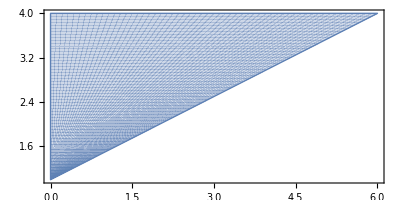

```mathematica
ParametricPlot[{(1-x)y,x},{x,1,4},{y,-2,0}]
```

```mathematica
Integrate[1/((√(-x+x1))^3(√(x-x2))^3),x]//FullSimplify
Integrate[-x/((√(-x+x1))^3(√(x-x2))^3),x]//FullSimplify
```

(4 x-2 (x1+x2))/(√(-x+x1) √(x-x2) (x1-x2)^2)

(4 x1 x2-2 x (x1+x2))/(√(-x+x1) √(x-x2) (x1-x2)^2)

```mathematica
Series[(4 x1 x2-2 x (x1+x2))/(√(-x+x1) √(x-x2) (x1-x2)^2),{x,∞,0}]
Series[(4 x1 x2-2 x (x1+x2))/(√(-x+x1) √(x-x2) (x1-x2)^2),{x,-∞,0}]
```

(2 ⅈ (x1+x2))/(x1-x2)^2+O[1/x]^1

-(2 (√x (x1+x2)))/(√-x (x1-x2)^2)+O[1/x]^1

```mathematica
Series[Integrate[-x/(√(x-x1)√(x-x2))^3,x],{x,∞,0}]
Series[Integrate[-x/(√(x-x1)√(x-x2))^3,x]/.x-> -y,{y,∞,0}]
```

(2 (x1+x2))/(x1-x2)^2+O[1/x]^1

(2 (x1+x2))/(x1-x2)^2+O[1/y]^1

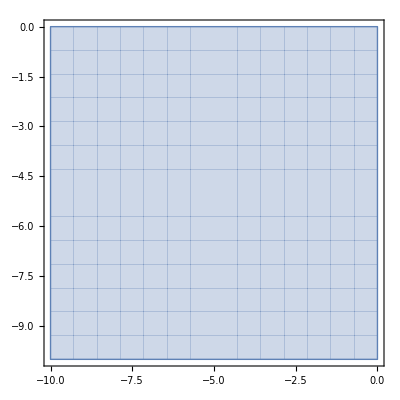

```mathematica
ParametricPlot[{x,y},{x,-10,0},{y,-10,0}]
```

```mathematica
L2 = Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3)/.{Subscript[x, 2]-> (1-Subscript[x, 1]-Subscript[x, 2])}/.{Subscript[x, 1]-> x,Subscript[x, 2]-> (1+x)y}
```

m1 x+m3 (1+x) y+k3^2 x (1+x) y+m2 (1-x-(1+x) y)+k1^2 x (1-x-(1+x) y)+k2^2 (1+x) y (1-x-(1+x) y)

```mathematica
L3= Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3)/.{Subscript[x, 2]-> (1-Subscript[x, 1]-Subscript[x, 2])}/.{Subscript[x, 1]-> x,Subscript[x, 2]-> (1-x)y}
```

m1 x+m3 (1-x) y+k3^2 (1-x) x y+m2 (1-x-(1-x) y)+k1^2 x (1-x-(1-x) y)+k2^2 (1-x) y (1-x-(1-x) y)

```mathematica
res2 = Integrate[(1+x)/L3^(3/2)/.{x-> -x},y]
```

(2 (1-x) (m2-m3-k1^2 x+k3^2 x+k2^2 (1+x) (-1+2 y)))/((1+x) (k2^4 (1+x)^2+(m2-m3+(-k1^2+k3^2) x)^2+2 k2^2 (m2 (1+x)+m3 (1+x)-x (2 m1+k1^2 (1+x)+k3^2 (1+x)))) √(-m1 x-m2 (1+x) (-1+y)+k1^2 x (1+x) (-1+y)+k2^2 y+m3 y+2 k2^2 x y-k3^2 x y+m3 x y+k2^2 x^2 y-k3^2 x^2 y-k2^2 y^2-2 k2^2 x y^2-k2^2 x^2 y^2))

```mathematica
res=Integrate[(1+x)/L2^(3/2),y]
```

(2 (m2-m3+k1^2 x-k3^2 x+k2^2 (-1+x+2 y+2 x y)))/((k2^4 (-1+x)^2+(m2-m3+(k1^2-k3^2) x)^2-2 k2^2 (m2 (-1+x)+m3 (-1+x)+(-2 m1+k1^2 (-1+x)+k3^2 (-1+x)) x)) √(m1 x+k2^2 y+m3 y+k3^2 x y+m3 x y-k2^2 x^2 y+k3^2 x^2 y-k2^2 y^2-2 k2^2 x y^2-k2^2 x^2 y^2-m2 (-1+x+y+x y)-k1^2 x (-1+x+y+x y)))

```mathematica
Normal[Series[res,{y,∞,0}]]-Normal[Series[res2/.y-> -y,{y,∞,0}]]
```

-((4 k2^2 (-1+x) y)/((k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2-2 k1^2 k2^2 x+2 k2^4 x-2 k2^2 k3^2 x-4 k2^2 m1 x-2 k1^2 m2 x+2 k2^2 m2 x+2 k3^2 m2 x+2 k1^2 m3 x+2 k2^2 m3 x-2 k3^2 m3 x+k1^4 x^2-2 k1^2 k2^2 x^2+k2^4 x^2-2 k1^2 k3^2 x^2-2 k2^2 k3^2 x^2+k3^4 x^2) √(-k2^2 (1+x)^2 y^2)))+(4 k2^2 (1+x) y)/((k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2+2 k1^2 k2^2 x-2 k2^4 x+2 k2^2 k3^2 x+4 k2^2 m1 x+2 k1^2 m2 x-2 k2^2 m2 x-2 k3^2 m2 x-2 k1^2 m3 x-2 k2^2 m3 x+2 k3^2 m3 x+k1^4 x^2-2 k1^2 k2^2 x^2+k2^4 x^2-2 k1^2 k3^2 x^2-2 k2^2 k3^2 x^2+k3^4 x^2) √(-k2^2 (1+x)^2 y^2))

```mathematica
Normal[Series[res2/.y-> -y,{y,∞,0}]]
```

(4 k2^2 (-1+x) y)/((k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2-2 k1^2 k2^2 x+2 k2^4 x-2 k2^2 k3^2 x-4 k2^2 m1 x-2 k1^2 m2 x+2 k2^2 m2 x+2 k3^2 m2 x+2 k1^2 m3 x+2 k2^2 m3 x-2 k3^2 m3 x+k1^4 x^2-2 k1^2 k2^2 x^2+k2^4 x^2-2 k1^2 k3^2 x^2-2 k2^2 k3^2 x^2+k3^4 x^2) √(-k2^2 (1+x)^2 y^2))

```mathematica
(L2/.{Subscript[x, 1]-> -Subscript[x, 1]})//Simplify
```

m2-k1^2 x_1^2+(k2^2-m2+m3) x_2-k2^2 x_2^2+x_1 (-k1^2-m1+m2+(k1^2+k2^2-k3^2) x_2)

```mathematica
(L2/.{Subscript[x, 2]-> -Subscript[x, 2]})//Simplify
```

m2-k1^2 x_1^2-(k2^2-m2+m3) x_2-k2^2 x_2^2+x_1 (k1^2+m1-m2+(k1^2+k2^2-k3^2) x_2)

```mathematica
Solve[Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3)==0,Subscript[x, 1]]
```

{{x_1→-(-k3^2-m1+m3-k1^2 x_2+k2^2 x_2+k3^2 x_2-√((k3^2+m1-m3+k1^2 x_2-k2^2 x_2-k3^2 x_2)^2+4 k3^2 (m3+k2^2 x_2+m2 x_2-m3 x_2-k2^2 x_2^2)))/(2 k3^2)},{x_1→-(-k3^2-m1+m3-k1^2 x_2+k2^2 x_2+k3^2 x_2+√((k3^2+m1-m3+k1^2 x_2-k2^2 x_2-k3^2 x_2)^2+4 k3^2 (m3+k2^2 x_2+m2 x_2-m3 x_2-k2^2 x_2^2)))/(2 k3^2)}}

```mathematica
(-k3^2-m1+m3-k1^2 Subscript[x, 2]+k2^2 Subscript[x, 2]+k3^2 Subscript[x, 2]-√((k3^2+m1-m3+k1^2 Subscript[x, 2]-k2^2 Subscript[x, 2]-k3^2 Subscript[x, 2])^2+4 k3^2 (m3+k2^2 Subscript[x, 2]+m2 Subscript[x, 2]-m3 Subscript[x, 2]-k2^2 Subscript[x, 2]^2)))/(2 k3^2)/.Subscript[x, 2]-> 1
```

(-k1^2+k2^2-m1-√(4 k3^2 m2+(k1^2-k2^2+m1-m3)^2)+m3)/(2 k3^2)

```mathematica
1-Subscript[x, 1]-Subscript[x, 2]/.{Subscript[x, 1]->x/(-1+2 x+2 y),Subscript[x, 2]->y/(-1+2 x+2 y)}//FullSimplify
```

(-1+x+y)/(-1+2 x+2 y)

```mathematica
II/.{Subscript[x, 1]->x/(-1+2 x+2 y),Subscript[x, 2]->y/(-1+2 x+2 y)}//FullSimplify
```

((k3^2+m1) x+(k2^2+m2) y+k1^2 x y-m3 (-1+x+y)-k3^2 x (x+y)-k2^2 y (x+y))/(-1+2 x+2 y)^2

```mathematica
II/.{Subscript[x, 1]->x/(-1+2 x+2 y),Subscript[x, 2]->y/(-1+2 x+2 y)}/.{x-> 1/a,y-> 1/b}//FullSimplify
```

(-b^2 k3^2+a b (k1^2-k2^2+(-1+b) k3^2+b (m1-m3))+a^2 ((-1+b) k2^2+b (m2+(-1+b) m3)))/(a (-2+b)-2 b)^2

```mathematica
ParametricPlot[]
```

```mathematica
(k3^2+m1) x+(k2^2+m2) y+k1^2 x y-m3 (-1+x+y)-k3^2 x (x+y)-k2^2 y (x+y)/.{x-> r Cos[θ],y-> r Sin[θ]}//Simplify
```

m3-k3^2 r^2 Cos[θ]^2+(k2^2+m2-m3) r Sin[θ]-k2^2 r^2 Sin[θ]^2-r Cos[θ] (-k3^2-m1+m3+(-k1^2+k2^2+k3^2) r Sin[θ])

```mathematica
(k3^2+m1) x+(k2^2+m2) y+k1^2 x y-m3 (-1+x+y)-k3^2 x (x+y)-k2^2 y (x+y)/.{x->r Sin[θ],y-> r Cos[θ]}//Simplify
```

m3-k2^2 r^2 Cos[θ]^2+(k3^2+m1-m3) r Sin[θ]-k3^2 r^2 Sin[θ]^2-r Cos[θ] (-k2^2-m2+m3+(-k1^2+k2^2+k3^2) r Sin[θ])

```mathematica
(k3^2+m1) x+(k2^2+m2) y+k1^2 x y-m3 (-1+x+y)-k3^2 x (x+y)-k2^2 y (x+y)/.{x-> -r Sin[θ],y-> -r Cos[θ]}//Simplify
```

m3-k2^2 r^2 Cos[θ]^2-(k3^2+m1-m3) r Sin[θ]-k3^2 r^2 Sin[θ]^2-r Cos[θ] (k2^2+m2-m3+(-k1^2+k2^2+k3^2) r Sin[θ])

```mathematica
ComplexExpand[(k3^2+M1-M3+k1^2 y-k2^2 y-k3^2 y)^2-4 k3^2(-M3-k2^2 y-M2 y+M3 y+k2^2 y^2),{M1,M2,M3}]
```

k3^4+2 k1^2 k3^2 y+2 k2^2 k3^2 y-2 k3^4 y+k1^4 y^2-2 k1^2 k2^2 y^2+k2^4 y^2-2 k1^2 k3^2 y^2-2 k2^2 k3^2 y^2+k3^4 y^2-Im[M1]^2+2 Im[M1] Im[M3]-Im[M3]^2+2 k3^2 Re[M1]+2 k1^2 y Re[M1]-2 k2^2 y Re[M1]-2 k3^2 y Re[M1]+Re[M1]^2+4 k3^2 y Re[M2]+2 k3^2 Re[M3]-2 k1^2 y Re[M3]+2 k2^2 y Re[M3]-2 k3^2 y Re[M3]-2 Re[M1] Re[M3]+Re[M3]^2+ⅈ (2 k3^2 Im[M1]+2 k1^2 y Im[M1]-2 k2^2 y Im[M1]-2 k3^2 y Im[M1]+4 k3^2 y Im[M2]+2 k3^2 Im[M3]-2 k1^2 y Im[M3]+2 k2^2 y Im[M3]-2 k3^2 y Im[M3]+2 Im[M1] Re[M1]-2 Im[M3] Re[M1]-2 Im[M1] Re[M3]+2 Im[M3] Re[M3])

```mathematica
Collect[Collect[2 k3^2 Im[M1]+2 k1^2 y Im[M1]-2 k2^2 y Im[M1]-2 k3^2 y Im[M1]+4 k3^2 y Im[M2]+2 k3^2 Im[M3]-2 k1^2 y Im[M3]+2 k2^2 y Im[M3]-2 k3^2 y Im[M3]+2 Im[M1] Re[M1]-2 Im[M3] Re[M1]-2 Im[M1] Re[M3]+2 Im[M3] Re[M3],Re[M3]],Re[M1]]
```

2 k3^2 Im[M1]+2 k1^2 y Im[M1]-2 k2^2 y Im[M1]-2 k3^2 y Im[M1]+4 k3^2 y Im[M2]+2 k3^2 Im[M3]-2 k1^2 y Im[M3]+2 k2^2 y Im[M3]-2 k3^2 y Im[M3]+(2 Im[M1]-2 Im[M3]) Re[M1]+(-2 Im[M1]+2 Im[M3]) Re[M3]

```mathematica
ArcTan[(√(x + z1))/(√(x + z0))/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ}]/.x-> -100000
```

-0.785397+6.2501×10^-6 ⅈ

```mathematica
Solve[m3+k3^2 x+m1 x-m3 x-k3^2 x^2+k2^2 y+m2 y-m3 y+k1^2 x y-k2^2 x y-k3^2 x y-k2^2 y^2==0,x]
```

{{x→-(-k3^2-m1+m3-k1^2 y+k2^2 y+k3^2 y-√((k3^2+m1-m3+k1^2 y-k2^2 y-k3^2 y)^2+4 k3^2 (m3+k2^2 y+m2 y-m3 y-k2^2 y^2)))/(2 k3^2)},{x→-(-k3^2-m1+m3-k1^2 y+k2^2 y+k3^2 y+√((k3^2+m1-m3+k1^2 y-k2^2 y-k3^2 y)^2+4 k3^2 (m3+k2^2 y+m2 y-m3 y-k2^2 y^2)))/(2 k3^2)}}

```mathematica
Solve[m3-k3^2 x-m1 x+m3 x-k3^2 x^2-k2^2 y-m2 y+m3 y+k1^2 x y-k2^2 x y-k3^2 x y-k2^2 y^2==0,y]
```

{{y→-(k2^2+m2-m3-k1^2 x+k2^2 x+k3^2 x-√((-k2^2-m2+m3+k1^2 x-k2^2 x-k3^2 x)^2+4 k2^2 (m3-k3^2 x-m1 x+m3 x-k3^2 x^2)))/(2 k2^2)},{y→-(k2^2+m2-m3-k1^2 x+k2^2 x+k3^2 x+√((-k2^2-m2+m3+k1^2 x-k2^2 x-k3^2 x)^2+4 k2^2 (m3-k3^2 x-m1 x+m3 x-k3^2 x^2)))/(2 k2^2)}}

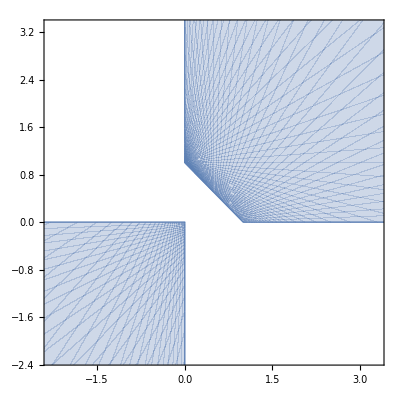

```mathematica
ParametricPlot[{x/(-1+2 x+2 y),y/(-1+2 x+2 y)},{y,0,1},{x,0,1-y}]
```

```mathematica
Solve[{t x == Subscript[s, 1],t(x-1) == Subscript[s, 2]},{x,t}]
```

{{x→s_1/(s_1-s_2),t→s_1-s_2}}

```mathematica
Integrate[q^(-1/2)Exp[ - A q],{q,0,∞}]
```

ConditionalExpression[(√π)/(√A), Re[A]>0]

```mathematica
test = Integrate[(Subscript[x, 1] Subscript[x, 2] k1^2 + Subscript[x, 2] Subscript[x, 3] k2^2+Subscript[x, 1] Subscript[x, 3] k3^2+(Subscript[x, 1] m1 + Subscript[x, 2] m2 + Subscript[x, 3] m3))^(-3/2)/.{Subscript[x, 3]-> 1-Subscript[x, 2]-Subscript[x, 1]},Subscript[x, 1]];testres = Collect[Integrate[Series[test,{Subscript[x, 1],∞,0},Assumptions->{k3>0,Subscript[x, 1]>0}],Subscript[x, 2]],Subscript[x, 2]]
```

-((2 ⅈ ArcTan[(k2^2 k3^2-k3^4-k2^2 m1-k3^2 m1+2 k3^2 m2+k1^2 (k3^2+m1-m3)+k2^2 m3-k3^2 m3+(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) x_2)/(2 k3 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))])/(√(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3)))))

```mathematica
Series[ArcTan[(k2^2 k3^2-k3^4-k2^2 m1-k3^2 m1+2 k3^2 m2+k1^2 (k3^2+m1-m3)+k2^2 m3-k3^2 m3+(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) Subscript[x, 2])/(2 k3 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))],{Subscript[x, 2],∞,0},Assumptions->{k3>0,k2>0,k1>0}]
```

$Aborted

```mathematica
test2 = Integrate[(Subscript[x, 1] Subscript[x, 2] k1^2 - Subscript[x, 2] Subscript[x, 3] k2^2-Subscript[x, 1] Subscript[x, 3] k3^2+(-Subscript[x, 1] m1 + -Subscript[x, 2] m2 + Subscript[x, 3] m3))^(-3/2)/.{Subscript[x, 3]-> 1+Subscript[x, 2]+Subscript[x, 1]},Subscript[x, 2]];
testres2 = Collect[Integrate[Series[test2,{Subscript[x, 2],∞,0},Assumptions->{k2>0,Subscript[x, 2]>0}],Subscript[x, 1]],Subscript[x, 1]]
```

-((2 ⅈ ArcTan[(k2^4-k2^2 k3^2-2 k2^2 m1+k2^2 m2+k3^2 m2-k1^2 (k2^2+m2-m3)+k2^2 m3-k3^2 m3+(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) x_1)/(2 k2 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))])/(√(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3)))))

```mathematica
Series[(k2^4-k2^2 k3^2-2 k2^2 m1+k2^2 m2+k3^2 m2-k1^2 (k2^2+m2-m3)+k2^2 m3-k3^2 m3+(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) Subscript[x, 1])/(2 k2 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3)))),{Subscript[x, 1],∞,0}]
```

((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) x_1)/(2 k2 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))+(k2^4-k2^2 k3^2-2 k2^2 m1+k2^2 m2+k3^2 m2-k1^2 (k2^2+m2-m3)+k2^2 m3-k3^2 m3)/(2 k2 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))+O[1/x_1]^1

```mathematica
testres + testres2/.Subscript[x, 2]-> 1//FullSimplify
```

-((2 ⅈ (ArcCot[(2 k3 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))/(k1^4+k2^4-k2^2 (k3^2+m1-m3)-k1^2 (2 k2^2+k3^2-m1+m3)-k3^2 (m1-2 m2+m3))]+ArcCot[(2 k3 √(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3))))/(k1^4+k2^4+k2^2 (-3 k3^2+m1-m3)-k1^2 (2 k2^2+3 k3^2+m1-m3)+k3^2 (2 k3^2+m1-2 m2+m3))]))/(√(k2^4 m1+k3^4 m2-k2^2 (k3^2 (m1+m2)+(m1-m2) (m1-m3))+k3^2 (m1-m2) (m2-m3)+k1^4 m3-k1^2 ((m1-m3) (m2-m3)+k2^2 (k3^2+m1+m3)+k3^2 (m2+m3)))))

```mathematica
m1 x (-1+2 x)-(k2^2+m2) y+(k1^2+k2^2+2 (m1+m2)) x y+(k2^2+2 m2) y^2+k3^2 x (-1+x+y)+m3 (-1+x+y) (-1+2 x+2 y)//Expand
```

m3-k3^2 x-m1 x-3 m3 x+k3^2 x^2+2 m1 x^2+2 m3 x^2-k2^2 y-m2 y-3 m3 y+k1^2 x y+k2^2 x y+k3^2 x y+2 m1 x y+2 m2 x y+4 m3 x y+k2^2 y^2+2 m2 y^2+2 m3 y^2

```mathematica
RRR2 = (1-x)/L2^(3/2)//Simplify
```

(1-x)/((m1 x+m3 (-1+x) (-1+y)+k3^2 (-1+x) x (-1+y)-m2 (-1+x) y-k1^2 (-1+x) x y-k2^2 (-1+x)^2 (-1+y) y)^(3/2))

```mathematica
PPP2 = Integrate[RRR2,y]//Simplify
```

-((2 (m2-m3+k1^2 x-k3^2 x+k2^2 (-1+x) (-1+2 y)))/((k2^4 (-1+x)^2+(m2-m3+(k1^2-k3^2) x)^2-2 k2^2 (m2 (-1+x)+m3 (-1+x)+(-2 m1+k1^2 (-1+x)+k3^2 (-1+x)) x)) √(m1 x+m3 (-1+x) (-1+y)+k3^2 (-1+x) x (-1+y)+k2^2 y+m2 y+k1^2 x y-2 k2^2 x y-m2 x y-k1^2 x^2 y+k2^2 x^2 y-k2^2 y^2+2 k2^2 x y^2-k2^2 x^2 y^2)))

```mathematica
dem =Collect[Expand[(k2^4 (-1+x)^2+(m2-m3+(k1^2-k3^2) x)^2-2 k2^2 (m2 (-1+x)+m3 (-1+x)+(-2 m1+k1^2 (-1+x)+k3^2 (-1+x)) x)) ],x]
```

k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2+(2 k1^2 k2^2-2 k2^4+2 k2^2 k3^2+4 k2^2 m1+2 k1^2 m2-2 k2^2 m2-2 k3^2 m2-2 k1^2 m3-2 k2^2 m3+2 k3^2 m3) x+(k1^4-2 k1^2 k2^2+k2^4-2 k1^2 k3^2-2 k2^2 k3^2+k3^4) x^2

```mathematica
rhoD = (k1-k2+k3)(k1+k2+k3)(k1-k2-k3)(k1+k2-k3);
cc =( k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2)/rhoD;
x1 = (2 k1^2 k2^2-2 k2^4+2 k2^2 k3^2+4 k2^2 m1+2 k1^2 m2-2 k2^2 m2-2 k3^2 m2-2 k1^2 m3-2 k2^2 m3+2 k3^2 m3)/rhoD/2//Simplify;
dem1 = x1^2-cc;
```

```mathematica
rhoD((x+x1)^2-dem1)-dem//Simplify
```

0

```mathematica
dem2 = Collect[Expand[(m1 x+m3 (-1+x) (-1+y)+k3^2 (-1+x) x (-1+y)+k2^2 y+m2 y+k1^2 x y-2 k2^2 x y-m2 x y-k1^2 x^2 y+k2^2 x^2 y-k2^2 y^2+2 k2^2 x y^2-k2^2 x^2 y^2) ],x]
```

m3+k2^2 y+m2 y-m3 y-k2^2 y^2+x^2 (-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2)+x (k3^2+m1-m3+k1^2 y-2 k2^2 y-k3^2 y-m2 y+m3 y+2 k2^2 y^2)

```mathematica
rhoS =-(-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2);
ccc = -(m3+k2^2 y+m2 y-m3 y-k2^2 y^2)/rhoS;
x0 = -(k3^2+m1-m3+k1^2 y-2 k2^2 y-k3^2 y-m2 y+m3 y+2 k2^2 y^2)/rhoS/2;
demR = x0^2-ccc;
```

```mathematica
rhoS(-(x+x0)^2+demR)-dem2//Simplify
```

0

```mathematica
rhoN = (k1^2-k3^2+k2^2 (-1+2 y));
c = (m2-m3-k2^2 (-1+2 y))/rhoN;
```

```mathematica
(-2 rhoN(x+c))/(√(rhoS (-(x+x0)^2+demR))rhoD((x+x1)^2-dem1))/PPP2//Simplify
```

1

```mathematica
Clear[rhoN,c,x0,x1,demR,dem1,rhoS,rhoD]
```

```mathematica
babisresult = -((rhoN √(demR-(x+x0)^2) (((c+√dem1-x1) ArcTan[(demR-(x+x0) (√dem1+x0-x1))/(√(demR-(x+x0)^2) √(dem1-demR+2 √dem1 (x0-x1)+(x0-x1)^2))])/(√(dem1-demR+2 √dem1 (x0-x1)+(x0-x1)^2))+((-c+√dem1+x1) ArcTan[(demR+(x+x0) (√dem1-x0+x1))/(√(demR-(x+x0)^2) √(dem1-demR-2 √dem1 (x0-x1)+(x0-x1)^2))])/(√(dem1-demR-2 √dem1 (x0-x1)+(x0-x1)^2))))/(√dem1 rhoD √(rhoS (demR-(x+x0)^2))));
```

```mathematica
Series[babisresult,{x,∞,0},Assumptions->{k1^2>0,k2^2>0,k3^2>0,y>0}]
```

$Aborted

```mathematica
L=II/.{Subscript[x, 2]-> (1-Subscript[x, 1])y}/.{Subscript[x, 1]-> x}
```

k1^2 (1-x) x y-k3^2 x (1-x-(1-x) y)-k2^2 (1-x) y (1-x-(1-x) y)+(m1 x+m2 (1-x) y-m3 (1-x-(1-x) y)) (-1+2 (x+(1-x) y))

```mathematica
RRR=(1-x)/L^(3/2)//Simplify
```

(1-x)/(-k3^2 (-1+x) x (-1+y)-k1^2 (-1+x) x y+k2^2 (-1+x)^2 (-1+y) y+(1+2 x (-1+y)-2 y) (-m1 x+m3 (-1+x) (-1+y)+m2 (-1+x) y))^(3/2)

```mathematica
PPP=Integrate[RRR,y]//Simplify
```

-((2 (-3 m3+k1^2 x+k3^2 x+2 m1 x+4 m3 x+4 m3 y-4 m3 x y+m2 (-1+2 x+4 y-4 x y)+k2^2 (-1+x+2 y-2 x y)))/((m3^2+m2^2 (1-2 x)^2+k2^4 (-1+x)^2-6 k1^2 m3 x+2 k3^2 m3 x-4 m1 m3 x+k1^4 x^2+2 k1^2 k3^2 x^2+k3^4 x^2+4 k1^2 m1 x^2+4 k3^2 m1 x^2+4 m1^2 x^2+8 k1^2 m3 x^2+m2 m3 (-2+4 x)+2 m2 x (2 m1+k3^2 (3-2 x)-4 m1 x+k1^2 (-1+2 x))+2 k2^2 (m3-m3 x+x (k3^2+k1^2 (-1+x)-k3^2 x-2 m1 x)+m2 (1-3 x+2 x^2))) √(-m1 x+2 m1 x^2+m3 (-1+x) (1+2 x (-1+y)-2 y) (-1+y)-k2^2 y-m2 y+k1^2 x y+2 k2^2 x y+2 m1 x y+3 m2 x y-k1^2 x^2 y-k2^2 x^2 y-2 m1 x^2 y-2 m2 x^2 y+k2^2 y^2+2 m2 y^2-2 k2^2 x y^2-4 m2 x y^2+k2^2 x^2 y^2+2 m2 x^2 y^2+k3^2 x (-1+x+y-x y))))

```mathematica
dem =Collect[Expand[(m3^2+m2^2 (1-2 x)^2+k2^4 (-1+x)^2-6 k1^2 m3 x+2 k3^2 m3 x-4 m1 m3 x+k1^4 x^2+2 k1^2 k3^2 x^2+k3^4 x^2+4 k1^2 m1 x^2+4 k3^2 m1 x^2+4 m1^2 x^2+8 k1^2 m3 x^2+m2 m3 (-2+4 x)+2 m2 x (2 m1+k3^2 (3-2 x)-4 m1 x+k1^2 (-1+2 x))+2 k2^2 (m3-m3 x+x (k3^2+k1^2 (-1+x)-k3^2 x-2 m1 x)+m2 (1-3 x+2 x^2)))  ],x]
```

k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2+(-2 k1^2 k2^2-2 k2^4+2 k2^2 k3^2-2 k1^2 m2-6 k2^2 m2+6 k3^2 m2+4 m1 m2-4 m2^2-6 k1^2 m3-2 k2^2 m3+2 k3^2 m3-4 m1 m3+4 m2 m3) x+(k1^4+2 k1^2 k2^2+k2^4+2 k1^2 k3^2-2 k2^2 k3^2+k3^4+4 k1^2 m1-4 k2^2 m1+4 k3^2 m1+4 m1^2+4 k1^2 m2+4 k2^2 m2-4 k3^2 m2-8 m1 m2+4 m2^2+8 k1^2 m3) x^2

```mathematica
rhoN = (k1^2+k2^2+k3^2+2 m1+2 m2+4 m3-2 k2^2 y-4 m2 y-4 m3 y);
c = (-k2^2-m2-3 m3+2 k2^2 y+4 m2 y+4 m3 y)/rhoN;
```

```mathematica
rhoD = k1^4+(k2^2-k3^2-2 m1+2 m2)^2+2 k1^2 (k2^2+k3^2+2 (m1+m2+2 m3));
cc = (k2^4+2 k2^2 m2+m2^2+2 k2^2 m3-2 m2 m3+m3^2)/rhoD;
x1 = (-2 k1^2 k2^2-2 k2^4+2 k2^2 k3^2-2 k1^2 m2-6 k2^2 m2+6 k3^2 m2+4 m1 m2-4 m2^2-6 k1^2 m3-2 k2^2 m3+2 k3^2 m3-4 m1 m3+4 m2 m3)/rhoD/2;
dem1 = x1^2-cc;
```

```mathematica
rhoD((x+x1)^2-dem1)-dem//Simplify
```

0

```mathematica
dem2=Collect[(-m1 x+2 m1 x^2+m3 (-1+x) (1+2 x (-1+y)-2 y) (-1+y)-k2^2 y-m2 y+k1^2 x y+2 k2^2 x y+2 m1 x y+3 m2 x y-k1^2 x^2 y-k2^2 x^2 y-2 m1 x^2 y-2 m2 x^2 y+k2^2 y^2+2 m2 y^2-2 k2^2 x y^2-4 m2 x y^2+k2^2 x^2 y^2+2 m2 x^2 y^2+k3^2 x (-1+x+y-x y)),x]
```

-m3 (-1+y)-k2^2 y-m2 y+2 m3 (-1+y) y+k2^2 y^2+2 m2 y^2+x (-k3^2-m1+m3 (-1+y)-2 m3 (-1+y)^2+k1^2 y+2 k2^2 y+k3^2 y+2 m1 y+3 m2 y-2 m3 (-1+y) y-2 k2^2 y^2-4 m2 y^2)+x^2 (k3^2+2 m1+2 m3 (-1+y)^2-k1^2 y-k2^2 y-k3^2 y-2 m1 y-2 m2 y+k2^2 y^2+2 m2 y^2)

```mathematica
rhoS = -(k3^2+2 m1+2 m3 (-1+y)^2-k1^2 y-k2^2 y-k3^2 y-2 m1 y-2 m2 y+k2^2 y^2+2 m2 y^2);
ccc = -(-m3 (-1+y)-k2^2 y-m2 y+2 m3 (-1+y) y+k2^2 y^2+2 m2 y^2)/rhoS;
x0 = -(-k3^2-m1+m3 (-1+y)-2 m3 (-1+y)^2+k1^2 y+2 k2^2 y+k3^2 y+2 m1 y+3 m2 y-2 m3 (-1+y) y-2 k2^2 y^2-4 m2 y^2)/rhoS/2;
demR = x0^2-ccc;
```

```mathematica
rhoS(-(x+x0)^2+demR)-dem2//Simplify
```

0

```mathematica
(-2 rhoN(x+c))/(√(rhoS (-(x+x0)^2+demR))rhoD((x+x1)^2-dem1))/PPP//Simplify
```

1

```mathematica
Integrate[(-2 rhoN(x+c))/(√(rhoS (-(x+x0)^2+demR))rhoD((x+x1)^2-dem1)),x]
```

$Aborted

```mathematica
TrNk[n1_,n2_,n3_,k1_,k2_,k3_,M1_,M2_,M3_]:=Module[{k1vec,k2vec,qvec,k1mqvec,k2pqvec,ν2},
k1vec=k1{0,0,1};
ν2=(1/(2k1 k2))(k3^2-k2^2-k1^2);
k2vec=k2{0,√(1-ν2^2),ν2};
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
(1/π^(3/2))NIntegrate[q^2/((k1mqvec.k1mqvec+M1)^n1(qvec.qvec+M2)^n2(k2pqvec.k2pqvec+M3)^n3),{q,0,10000},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];
```

```mathematica
k1 = 0.2;
k2 = 0.3;
k3 = 0.4;
m1 = 0.3 + 0.1ⅈ;
m2 = 0.2 +0.15ⅈ;
m3 = 0.5-0.2ⅈ;
TrNk[1,1,1,k1,k2,k3,m1,m2,m3]
```

1.95571-0.416672 ⅈ

```mathematica
fint[X_,Y_]:=babisresult/.{x-> X,y-> Y}
```

```mathematica
(fint[1,1]+fint[0,0]-fint[1,0]-fint[0,1])/2 √π
```

-18.7594-13.6369 ⅈ

```mathematica
fin = Integrate[1/II^(3/2),Subscript[x, 2]]/.{Subscript[x, 2]-> y,Subscript[x, 1]-> x}
```

(2 (k2^2+m2+3 m3-(k1^2+k2^2+k3^2+2 m1+2 m2+4 m3) x-2 (k2^2+2 (m2+m3)) y))/((k2^4+(m2-m3)^2+2 k2^2 (m2+m3)-2 (k2^4-3 k3^2 m2-2 m1 m2+2 m2^2-k3^2 m3+2 m1 m3-2 m2 m3+k2^2 (-k3^2+3 m2+m3)+k1^2 (k2^2+m2+3 m3)) x+(k1^4+(k2^2-k3^2-2 m1+2 m2)^2+2 k1^2 (k2^2+k3^2+2 (m1+m2+2 m3))) x^2) √(m3+(k3^2+2 (m1+m3)) x^2-(k2^2+m2+3 m3) y+(k2^2+2 (m2+m3)) y^2+x (-k3^2-m1-3 m3+(k1^2+k2^2+k3^2+2 m1+2 m2+4 m3) y)))

```mathematica
(fin/.y-> 1-x)-(fin/.{y-> 0})//Simplify
```

(2 ((-m3+k2^2 (-1+x)-k1^2 x-k3^2 x-2 m1 x+m2 (-3+2 x))/(√(m2-m2 x+(m1-k1^2 (-1+x)) x))-(k2^2+m2+3 m3-(k1^2+k2^2+k3^2+2 m1+2 m2+4 m3) x)/(√(k3^2 (-1+x) x+m1 x (-1+2 x)+m3 (1-3 x+2 x^2)))))/(k2^4+(m2-m3)^2+2 k2^2 (m2+m3)-2 (k2^4-3 k3^2 m2-2 m1 m2+2 m2^2-k3^2 m3+2 m1 m3-2 m2 m3+k2^2 (-k3^2+3 m2+m3)+k1^2 (k2^2+m2+3 m3)) x+(k1^4+(k2^2-k3^2-2 m1+2 m2)^2+2 k1^2 (k2^2+k3^2+2 (m1+m2+2 m3))) x^2)

```mathematica
II =(Subscript[x, 1] Subscript[x, 2] k1^2 - Subscript[x, 2] Subscript[x, 3] k2^2-Subscript[x, 1] Subscript[x, 3] k3^2)/(Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3])+(Subscript[x, 1] m1 + Subscript[x, 2] m2 - Subscript[x, 3] m3);
```

```mathematica
pvint = Integrate[(1-Subscript[x, 1])/(Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3])^(3/2)1/II^(3/2)/.{Subscript[x, 3]->(1-Subscript[x, 1])(1-l2),Subscript[x, 2]-> (1-Subscript[x, 1])l2},l2]/.{Subscript[x, 1]-> x, l2-> y}//Simplify
```

(2 (1-x) (-3 m3+k1^2 x+k3^2 x+2 m1 x+4 m3 x+4 m3 y-4 m3 x y+m2 (-1+2 x+4 y-4 x y)+k2^2 (-1+x+2 y-2 x y)))/((-1+x) (k2^4+(m2-m3)^2+2 k2^2 (m2+m3)-2 (k2^4-3 k3^2 m2-2 m1 m2+2 m2^2-k3^2 m3+2 m1 m3-2 m2 m3+k2^2 (-k3^2+3 m2+m3)+k1^2 (k2^2+m2+3 m3)) x+(k1^4+(k2^2-k3^2-2 m1+2 m2)^2+2 k1^2 (k2^2+k3^2+2 (m1+m2+2 m3))) x^2) √(-1-2 x (-1+y)+2 y) √(1/(1+2 x (-1+y)-2 y)(-k2^2 (-1+y) y-(-1+2 y) (m3 (-1+y)+m2 y)+x (m1+3 m3-k3^2 (-1+y)-k1^2 y-2 k2^2 y-2 m1 y-3 m2 y-7 m3 y+2 k2^2 y^2+4 m2 y^2+4 m3 y^2)+x^2 (k3^2 (-1+y)+k1^2 y-(-1+y) (-2 m1+2 m3 (-1+y)+(k2^2+2 m2) y)))))

```mathematica
1/(Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3])/.{Subscript[x, 3]-> (1-x)(1-y),Subscript[x, 2]-> (1-x)y,Subscript[x, 1]-> x}//Simplify
```

1/(-1+2 x+2 y-2 x y)

```mathematica
(k1^2+M1+M2)(k1^2+M2-M1)//Expand
```

```mathematica
RegionPlot[Subscript[x, 1]/(2(Subscript[x, 1]+Subscript[x, 2])-1),{Subscript[x, 1],0,1},{Subscript[x, 2],0,1}]
```

-Graphics-

```mathematica
Solve[{Subscript[x, 1]/(2(Subscript[x, 1]+Subscript[x, 2])-1)==x,Subscript[x, 2]/(2(Subscript[x, 1]+Subscript[x, 2])-1)==y},{Subscript[x, 1],Subscript[x, 2]}]
```

{{x_1→x/(-1+2 x+2 y),x_2→y/(-1+2 x+2 y)}}

```mathematica
Solve[y/(-1+2 x+2 y)==0/.{x-> 0},y]
Solve[y/(-1+2(1/2-y-1/ϵ)+2 y)==0,y]
```

{{y→0}}

```mathematica
RegionPlot[Subscript[x, 1]/(2(Subscript[x, 1]+Subscript[x, 2])-1)&&Subscript[x, 1]+Subscript[x, 2]<1,{Subscript[x, 1],-100,1},{Subscript[x, 2],-100,1-Subscript[x, 1]}]
```

-Graphics-

```mathematica
Solve[y/(-1+2 x+2 y)==0/.{x-> 0},y]
Solve[y/(-1+2 y)==1,y]
Solve[y/(-1+2(1/2-y-1/ϵ)+2 y)==0,y]
Solve[y/(-1+2(1/2-y-1/ϵ)+2 y)==1,y]
```

{{y→0}}

{{y→1}}

{{y→0}}

{{y→-2/ϵ}}

```mathematica
Solve[y/(-1+2 (1-y)+2 y)==0,y]
Solve[y/(-1+2(1/2-y+1/ϵ)+2 y)==0,y]
Solve[y/(-1+2 (1-y)+2 y)==1,y]
Solve[y/(-1+2(1/2-y+1/ϵ)+2 y)==1,y]
```

{{y→0}}

{{y→0}}

{{y→1}}

{{y→2/ϵ}}

```mathematica
(pvint/.y-> 1)-(pvint/.y-> 0)//Simplify
```

(2 (1-x) ((m3+m2 (3-2 x)-k2^2 (-1+x)+k1^2 x+k3^2 x+2 m1 x)/(√(m2-m2 x+(m1-k1^2 (-1+x)) x))+(m2+3 m3-k2^2 (-1+x)-k1^2 x-k3^2 x-2 m1 x-2 m2 x-4 m3 x)/(√(-1+2 x) √((k3^2 (-1+x) x+m1 x (-1+2 x)+m3 (1-3 x+2 x^2))/(-1+2 x)))))/((-1+x) (k2^4+(m2-m3)^2+2 k2^2 (m2+m3)-2 (k2^4-3 k3^2 m2-2 m1 m2+2 m2^2-k3^2 m3+2 m1 m3-2 m2 m3+k2^2 (-k3^2+3 m2+m3)+k1^2 (k2^2+m2+3 m3)) x+(k1^4+(k2^2-k3^2-2 m1+2 m2)^2+2 k1^2 (k2^2+k3^2+2 (m1+m2+2 m3))) x^2))

```mathematica
Apart[(x + c)/((x - SubPlus[x])(x - SubMinus[x])),x]
```

(c+x_-)/((x-x_-) (x_--x_+))+(-c-x_+)/((x-x_+) (x_--x_+))

```mathematica
D[x/(√(2(x+y)-1)),x]//Simplify
D[x/(√(2(x+y)-1)),y]//Simplify
D[y/(√(2(x+y)-1)),x]//Simplify
D[y/(√(2(x+y)-1)),y]//Simplify
```

(2 (-1+x+2 y))/(-1+2 x+2 y)^(3/2)

-x/(-1+2 (x+y))^(3/2)

-y/(-1+2 (x+y))^(3/2)

(-1+2 x+y)/(-1+2 x+2 y)^(3/2)

```mathematica
(-1+x+2 y)/(-1+2 x+2 y)^(3/2)(-1+2 x+y)/(-1+2 x+2 y)^(3/2)-x/(-1+2 (x+y))^(3/2)y/(-1+2 (x+y))^(3/2)//Simplify
```

(-1+x+y)/(-1+2 x+2 y)^2

```mathematica
NIntegrate[1/(√(-(z-z1)(z-z0)))^1/.{z1-> 2.1 -2 ⅈ,z0-> 1.5+2ⅈ},{z,-10^8,10^8},WorkingPrecision->35]
NIntegrate[1/(√(-(z-z1)(z-z0)))^1/.{z-> ⅈ z}/.{z1-> 2.1 -2 ⅈ,z0-> 1.5+2ⅈ},{z,-10^8,10^8},WorkingPrecision->35]
```

3.2808461965388956810840363461033682×10^-6+21.333392457084689258716725150711673 ⅈ

21.325819897482043022536236382647432-0.0075554517624894100349644818787394348 ⅈ

```mathematica
NIntegrate[1/(√(-(z+z1)(z-z0)))^1/.{z1-> 2.1 -2 ⅈ,z0-> 1.5-2ⅈ,z-> -2ⅈ + rez-ⅈ 0.0001},{rez,-10^6,2.1},WorkingPrecision->15]
```

2.3051921094356+12.8610407523686 ⅈ

```mathematica
NIntegrate[1/(√(-(z+z1)(z-z0)))^1/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ,z-> -2ⅈ + rez+ⅈ 0.0001},{rez,2.1,-10^6},WorkingPrecision->15]
```

-2.6559645912107-13.1489266958894 ⅈ

```mathematica
ComplexExpand[-(x-x1)(x-x0),{x1,x0}]
```

-x^2+Im[x0] Im[x1]+x Re[x0]+x Re[x1]-Re[x0] Re[x1]+ⅈ (x Im[x0]+x Im[x1]-Im[x1] Re[x0]-Im[x0] Re[x1])

```mathematica
ComplexPlot[1/(√(-(z-z1))√(z-z0))^1/.{z1-> 2.1 -2 ⅈ,z0-> 1.5+2ⅈ},{z,3}]
```

-Graphics-

```mathematica
Integrate[1/((x-x3)(x-x4)),x]
```

(Log[x-x3]-Log[x-x4])/(x3-x4)

```mathematica
Integrate[1/((x-x3)(*(x-x4)*))/.{x3-> 3-3.ⅈ,x4-> 1.5+2ⅈ},x]/.x-> 0
```

1.44519+2.35619 ⅈ

```mathematica
Log[x-x3]/.{x3-> 3+3.ⅈ,x4-> 1.5+2ⅈ}/.x-> 0
```

1.44519-2.35619 ⅈ

```mathematica
Integrate[1/((x-x3)(x-x4)),{x,-∞,0}]/.{x3->- 100+3.ⅈ,x4-> -150+2ⅈ}/.x-> 0
(Log[Abs[x3]]-Log[Abs[x4]]+ⅈ Arg[-x3]-ⅈ Arg[-x4])/(x3-x4)(*+(2π ⅈ)/(x3-x4)*)/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}/.x-> 0
(Log[x3]-Log[x4])/(x3-x4)(*+(ⅈ Arg[-x3]-ⅈ Arg[-x4])/(x3-x4)*)/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}/.x-> 0
(Log[-x3]-Log[-x4])/(x3-x4)-(ⅈ Arg[-x3]-ⅈ Arg[-x4])/(x3-x4)/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}/.x-> 0
```

-0.00810551-0.000171059 ⅈ

-0.00810551-0.000171059 ⅈ

-0.00810551-0.000171059 ⅈ

-0.00809884+0.000161977 ⅈ

```mathematica
(Log[x3]-Log[x4])/(x3-x4)/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}
(Log[-x3]-Log[-x4])/(x3-x4)/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}
ⅈ Arg[-x3]-ⅈ Arg[-x4]/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}
ⅈ Arg[-x3]/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}//N
ⅈ Arg[-x4]/.{x3->-100+3.ⅈ,x4-> -150+2ⅈ}//N
```

-0.00810551-0.000171059 ⅈ

-0.00810551-0.000171059 ⅈ

0.-0.0166585 ⅈ

0.-0.029991 ⅈ

0.-0.0133325 ⅈ

```mathematica
Integrate[1/((x-x3)(x-x4)),{x,-∞,0},Assumptions->{Re[x4]<0,Re[x3]<0}]
Integrate[1/((x-x3)(x-x4)),{x,0,∞}]
```

ConditionalExpression[(Log[x3]-Log[x4])/(x3-x4), x3∉ℝ&&x4∉ℝ]

ConditionalExpression[(-Log[-x3]+Log[-x4])/(x3-x4), (Re[x3]<0||x3∉ℝ)&&(Re[x4]<0||x4∉ℝ)]

```mathematica
(Log[Abs[x3]]-Log[Abs[x4]]+ⅈ Arg[x3]-ⅈ Arg[x4])/(x3-x4)(*+(2π ⅈ)/(x3-x4)*)/.{x3->100+3.ⅈ,x4-> 150-2ⅈ}/.x-> 0
Integrate[1/((x-x3)(x-x4))/.{x3-> 100+3.ⅈ,x4-> 150-2ⅈ},{x,-∞,0}]
-(Log[Abs[x-x3]]-Log[Abs[x-x4]]+ⅈ Arg[-x3]-ⅈ Arg[-x4])/(x3-x4)(*+(2π ⅈ)/(x3-x4)*)/.{x3->100+3.ⅈ,x4-> 150-2ⅈ}/.x-> 0
Integrate[1/((x-x3)(x-x4))/.{x3-> 100+3.ⅈ,x4-> 150-2ⅈ},{x,0,∞}]
```

0.00810765-0.0000557055 ⅈ

0.00810765-0.0000557055 ⅈ

0.0043343-0.124364 ⅈ

0.0043343-0.124364 ⅈ

```mathematica
Arg[x4]/.{x3->-100-3.ⅈ,x4-> -150+2ⅈ}//N
 Arg[-x4]/.{x3->-100-3.ⅈ,x4-> -150+2ⅈ}//N
 Arg[x4]/.{x3->-100-3.ⅈ,x4-> -150-2ⅈ}//N
 Arg[-x4]/.{x3->-100-3.ⅈ,x4-> -150-2ⅈ}//N
```

3.12826

-0.0133325

-3.12826

0.0133325

```mathematica
Log[x4]-Log[-x4]/.{x3->-100-3.ⅈ,x4-> -150-2ⅈ}//N
Log[x4]-Log[-x4]/.{x3->-100-3.ⅈ,x4-> -150+2ⅈ}//N
```

0.-3.14159 ⅈ

0.+3.14159 ⅈ

```mathematica
Arg[x4]-Arg[-x4]/.{x4-> -150+2ⅈ}//N
Arg[x4]-Arg[-x4]/.{x4-> -150-2ⅈ}//N
```

3.14159

-3.14159

```mathematica
Log[x3]-Log[x4](*+(2π ⅈ)/(x3-x4)*)/.{x3->100+3.ⅈ,x4-> -150-2ⅈ}
Log[-x3]-Log[-x4](*+(2π ⅈ)/(x3-x4)*)/.{x3->100+3.ⅈ,x4-> -150-2ⅈ}
```

-0.405104+3.15825 ⅈ

-0.405104-3.12493 ⅈ

```mathematica
Log[Abs[-x4]]+ⅈ Arg[x4]/.{x3->100+3.ⅈ,x4-> 150-2ⅈ}//N
Log[-x4]/.{x3->100+3.ⅈ,x4-> 150-2ⅈ}//N
```

5.01072-0.0133325 ⅈ

5.01072+3.12826 ⅈ

```mathematica
Apart[1/((x-x3)(x-x4)),x]
```

1/((x-x3) (x3-x4))+1/((x-x4) (-x3+x4))

```mathematica
ComplexPlot[1/((x-x3)(x-x4))/.{x3-> 1+3.ⅈ,x4->- 1.5-2ⅈ},{x,10}]
```

-Graphics-

```mathematica
ComplexPlot[1/((x-x3)(x-x4))/.{x3-> 3-3.ⅈ,x4-> 1.5+2ⅈ},{x,3}]
```

-Graphics-

```mathematica
res = Integrate[ⅈ/(√(-(z-z1))√(z-z0))/.z->(r Exp[ⅈ θ]),θ,Assumptions->{r>0}]
```

-(2 ArcTan[(√z0 √(-ⅇ^(ⅈ θ) r+z1))/(√(ⅇ^(ⅈ θ) r-z0) √z1)])/(√z0 √z1)

```mathematica
p1=Series[res/.{θ-> π/2},{r,∞,0},Assumptions->{r>0}]//FullSimplify
p2=Series[res/.{θ-> 0},{r,∞,0},Assumptions->{r>0}]//FullSimplify//Normal
p3=Series[res/.{θ-> -π/2},{r,∞,0},Assumptions->{r>0}]//FullSimplify
p4=Series[res/.{θ-> π},{r,∞,0},Assumptions->{r>0}]//FullSimplify//Normal
```

(2 ⅈ ArcTanh[(√z0)/(√z1)])/(√z0 √z1)

-(2 ⅈ ArcTanh[(√z0)/(√z1)])/(√z0 √z1)

-(2 ⅈ ArcTanh[(√z0)/(√z1)])/(√z0 √z1)

(2 ⅈ ArcTanh[(√z0)/(√z1)])/(√z0 √z1)

```mathematica
p1-p2+p3-p4
```

0

```mathematica
res = Integrate[1/(√((-z+z1)(z-z0)))^3,z,Assumptions->{y>0}]//FullSimplify
```

(4 z-2 (z0+z1))/(√((-z+z0) (z-z1)) (z0-z1)^2)

```mathematica
Series[res/.z-> -y,{y,∞,0}]
Series[res/.z-> 0,{y,∞,0}]
Series[res/.z-> y,{y,∞,0}]
Series[res/.z->0,{y,∞,0}]
```

(4 ⅈ)/(z0-z1)^2+O[1/y]^1

-(2 (z0+z1))/((z0-z1)^2 √(-z0 z1))

-(4 ⅈ)/(z0-z1)^2+O[1/y]^1

-(2 (z0+z1))/((z0-z1)^2 √(-z0 z1))

```mathematica
Series[res,{y,∞,0}]
Series[res/.y-> -w,{w,∞,0}]
```

(-1)^Floor[1/2-Arg[ⅈ y-z0]/(2 π)+Arg[z0-z1]/(2 π)] Floor[1/2-Arg[ⅈ y-z0]/(2 π)+Arg[z0-z1]/(2 π)] ((2 π √((ⅈ y)/(z0-z1)) √(z0-z1))/(√(-ⅈ y))+O[1/y]^1)+(-1)^Floor[1/2-Arg[ⅈ y-z0]/(2 π)+Arg[z0-z1]/(2 π)] (-(ⅈ √((ⅈ y)/(z0-z1)) √(z0-z1) (2 Log[2]+Log[ⅈ y]-Log[z0-z1]))/(√(-ⅈ y))+O[1/y]^1)

(-1)^Floor[1/2-Arg[-ⅈ w-z0]/(2 π)+Arg[z0-z1]/(2 π)] Floor[1/2-Arg[-ⅈ w-z0]/(2 π)+Arg[z0-z1]/(2 π)] ((2 π √(-(ⅈ w)/(z0-z1)) √(z0-z1))/(√(ⅈ w))+O[1/w]^1)+(-1)^Floor[1/2-Arg[-ⅈ w-z0]/(2 π)+Arg[z0-z1]/(2 π)] (-(ⅈ √(-(ⅈ w)/(z0-z1)) √(z0-z1) (2 Log[2]+Log[-ⅈ w]-Log[z0-z1]))/(√(ⅈ w))+O[1/w]^1)

```mathematica
NIntegrate[1/(√(-(z+z1)(z+z0)))^3/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,-10^6,10^6},WorkingPrecision->100,PrecisionGoal->100,AccuracyGoal->100]
```

-0.5236745985442163936261747268434487378535486028306463248022453176894919795081693926332503397247062761-0.01887500205692414132139690046459580784863199528031165870346852295564139833484396265132456646805588595 ⅈ

```mathematica
Series[res/.{z-> z1+ ⅈ ϵ},{ϵ,0,0}]//Normal
Series[res/.{z-> -rez},{rez,∞,0}]//Normal
Series[res/.{z-> rez},{rez,∞,0}]//Normal
```

(√2 (z0+3 z1))/((z0-z1)^2 √(-z1 (z0+z1)))

(4 ⅈ)/(z0-z1)^2

-(4 ⅈ)/(z0-z1)^2

```mathematica
res2 = Integrate[(ϵ Exp[ⅈ θ])/(√(-(z-z1))√(z-z0))^3/.{z-> z1 + ϵ Exp[ⅈ θ]},θ]
(ⅈ Series[(res2/.θ-> π/2) - (res2/.θ-> 0),{ϵ,0,0},Assumptions->{ϵ>0}]//FullSimplify)-(Series[res/.{z-> z1+ ⅈ ϵ},{ϵ,0,0}]//Normal)//FullSimplify
```

-(2 ⅈ (-z0+z1+2 ⅇ^(ⅈ θ) ϵ))/((z0-z1)^2 √(-ⅇ^(ⅈ θ) ϵ) √(-z0+z1+ⅇ^(ⅈ θ) ϵ))

(2 ⅈ)/((-z0+z1)^(3/2) √ϵ)+√O[ϵ]

```mathematica
res3 = Integrate[1/(√(-(z-z1)(z-z0)))^1,z]
```

(2 √(z-z0) √((z-z1)/(z0-z1)) √(-z0+z1) ArcSin[(√(z-z0))/(√(-z0+z1))])/(√(-((z-z0) (z-z1))))

```mathematica
res/.z->- rez//Simplify
```

-(2 (2 rez+z0+z1))/((z0-z1)^2 √(-((rez+z0) (rez+z1))))

```mathematica
res = Integrate[1/(√(-(z-z1)(z-z0)))^3,z]//Normal
Series[res/.z-> rez//Simplify ,{rez,0,0},Assumptions->{rez>0}]//Normal
Series[res/.z->- rez//Simplify ,{rez,0,0},Assumptions->{rez>0}]//Normal
```

(4 z-2 (z0+z1))/(√(-((z-z0) (z-z1))) (z0-z1)^2)

-(2 (z0+z1))/((z0-z1)^2 √(-z0 z1))

-(2 (z0+z1))/((z0-z1)^2 √(-z0 z1))

```mathematica
res = Integrate[1/(√(-(z-z1)(z-z0)))^3,z]
Series[res3/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,∞,0},Assumptions->{z>0}]//Normal
Series[res/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,∞,0},Assumptions->{z>0}]//Normal
Series[res3/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,-∞,0},Assumptions->{z<0}]//Normal
Series[res/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,-∞,0},Assumptions->{z<0}]//Normal
```

(4 z-2 (z0+z1))/(√(-((z-z0) (z-z1))) (z0-z1)^2)

(-6.28319+9.86076×10^-32 ⅈ) (-1)^Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]] Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]]+(1.2326×10^-32+1. ⅈ) (-1)^Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]] ((0.442003+1.80634 ⅈ)+(1.+0. ⅈ) Log[z])

0.274649-0.539228 ⅈ

(6.28319-9.86076×10^-32 ⅈ) (-1)^Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]] Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]]-(1.2326×10^-32+1. ⅈ) (-1)^Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]] ((0.442003+4.94793 ⅈ)+(1.+0. ⅈ) Log[-z])

0.274649-0.539228 ⅈ

```mathematica
(Series[res3/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,∞,0}]//Normal) - (Series[res3/.{z1-> 2.1 + 0.5ⅈ,z0-> 1.5-2ⅈ},{z,-∞,0}]//Normal)//FullSimplify
```

1/(√z)(-1)^Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]] √((-0.0907716+0.378215 ⅈ) z) ((1.23664-2.71327 ⅈ)+(6.23745-7.91157 ⅈ) Floor[0.212512-0.159155 Arg[(-1.5+2. ⅈ)+z]]-(1.25916+0.992722 ⅈ) Log[z])

```mathematica
s[a_,b_]:=(-1)^HeavisideTheta[-Im[a]](-1)^HeavisideTheta[-Im[b]](-1)^HeavisideTheta[Im[a b]](-1)^HeavisideTheta[Im[a]](-1)^HeavisideTheta[Im[b]](-1)^HeavisideTheta[-Im[a b]]
```

```mathematica
s[-(Re[x]-x1),(Re[x]-x0)]
```

(-1)^(HeavisideTheta[-Im[x0]]+HeavisideTheta[Im[x0]]+HeavisideTheta[-Im[x1]]+HeavisideTheta[Im[x1]]+HeavisideTheta[-Im[(x1-Re[x]) (-x0+Re[x])]]+HeavisideTheta[Im[(x1-Re[x]) (-x0+Re[x])]])

```mathematica
(-1)^(HeavisideTheta[-Im[(x1-Re[x]) (-x0+Re[x])]]+HeavisideTheta[Im[(x1-Re[x]) (-x0+Re[x])]])//Expand
```

```mathematica
ComplexExpand[(x1-x)(x-x0),{x1,x0}]
```

-x^2+Im[x0] Im[x1]+x Re[x0]+x Re[x1]-Re[x0] Re[x1]+ⅈ (x Im[x0]+x Im[x1]-Im[x1] Re[x0]-Im[x0] Re[x1])

```mathematica
x Im[x0]+x Im[x1]-Im[x1] Re[x0]-Im[x0] Re[x1]
-(x Im[x0]+x Im[x1]-Im[x1] Re[x0]-Im[x0] Re[x1])
```

x Im[x0]+x Im[x1]-Im[x1] Re[x0]-Im[x0] Re[x1]

-x Im[x0]-x Im[x1]+Im[x1] Re[x0]+Im[x0] Re[x1]

```mathematica
FullSimplify[s[-1+0.0001ⅈ,a],Assumptions->{Im[a]>0,Re[a]>0}]
```

(-1)^(HeavisideTheta[Im[(-1.+0.0001 ⅈ) a]]+HeavisideTheta[Im[(1.-0.0001 ⅈ) a]])

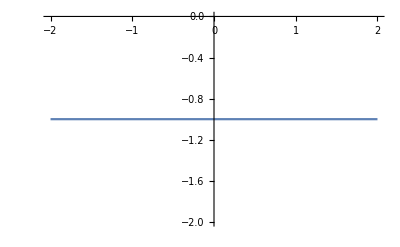

```mathematica
Plot[s[-(x +  2.1 + 0.5ⅈ),x + 1.5-2ⅈ],{x,-2,2}]
```

### Evaluation of Triangle Integral when conditions on s are not satisfied

```mathematica
int= M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x)//Expand
```

M3+k3^2 x+M1 x-M3 x-k3^2 x^2+k2^2 y+M2 y-M3 y+k1^2 x y-2 k2^2 x y-k3^2 x y-M2 x y+M3 x y-k1^2 x^2 y+k2^2 x^2 y+k3^2 x^2 y-k2^2 y^2+2 k2^2 x y^2-k2^2 x^2 y^2

```mathematica
Solve[int==0,y]
```

{{y→1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2-√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2))},{y→1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2+√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2))}}

```mathematica
suby = {y1->1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2-√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2)),
y2->1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2+√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2))};
```

```mathematica
(k2^2(1-x)^2(y1-y)(y-y2)/.suby)-int//FullSimplify
```

0

```mathematica
Clear[k2,y1,y2]
```

```mathematica
Series[Integrate[1/((√(k2^2(1-x)^2(y1-y)(y-y2)))^3),y,Assumptions->{k2>0,x<0,y<0}],y]//FullSimplify//Normal
```

(4 y-2 (y1+y2))/(k2^2 (-1+x)^2 √(k2^2 (-1+x)^2 (-y+y1) (y-y2)) (y1-y2)^2)

```mathematica
xres=Integrate[(ⅈ 4)/(k2^3 (-1+x)^3 (y1-y2)^2)/.suby,x]//FullSimplify
```

1/(4 k2^2 M1+(k1^2-k3^2+M2-M3)^2)2 ⅈ k2 (((-k1^4-k3^2 (k3^2-M2+M3)+k1^2 (k2^2+2 k3^2-M2+M3)+k2^2 (k3^2-2 M1+M2+M3)) ArcCot[(2 k2 √(k2^4 M1+k3^4 M2-k2^2 (k3^2 (M1+M2)+(M1-M2) (M1-M3))+k3^2 (M1-M2) (M2-M3)+k1^4 M3-k1^2 ((M1-M3) (M2-M3)+k2^2 (k3^2+M1+M3)+k3^2 (M2+M3))))/(k2^4 (-1+x)+k1^4 x+k3^2 (-M2+M3+k3^2 x)+k1^2 (k2^2+M2-M3-2 (k2^2+k3^2) x)-k2^2 (-2 M1+M2+M3+k3^2 (-1+2 x)))])/(k2 √(k2^4 M1+k3^4 M2-k2^2 (k3^2 (M1+M2)+(M1-M2) (M1-M3))+k3^2 (M1-M2) (M2-M3)+k1^4 M3-k1^2 ((M1-M3) (M2-M3)+k2^2 (k3^2+M1+M3)+k3^2 (M2+M3))))+2 Log[1-x]-Log[k2^4 (-1+x)^2+(M2-M3+(k1-k3) (k1+k3) x)^2+2 k2^2 (M2+M3+(k1^2+k3^2+2 M1) x-M2 x-x (M3+(k1^2+k3^2) x))])

```mathematica
xlim = Series[xres,{x,-∞,0}]
```

$Aborted